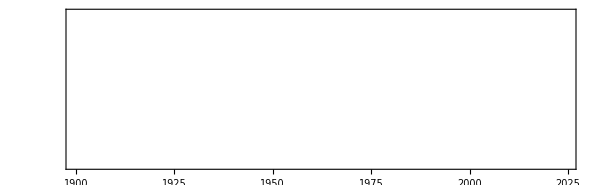

```mathematica
TimelinePlot[{Entity["Person","JuliusCaesar::wbbb2"],Entity["HistoricalCountry","RomanRepublic"], Entity["MilitaryConflict","FirstPunicWar"]}]
```

```mathematica
EntityValue["Person","Properties"]
```

{other names,astrological sign,date of birth,place of birth,brothers,place of burial,children,Chinese zodiac sign,daughters,date of death,place of death,educated at,entity classes,entity type list,father,full name,gender,height,husbands,image,killed by,languages spoken, written, or signed,space missions,mathematical contributions,mother,notable film appearances,notable film direction credits,notable film production credits,notable film writing credits,name,nationality,net worth,notable artworks,astronomical discoveries,notable books,famous chemistry problems,notable facts,notable inventions,physics contributions,occupation,parents,pets,place of residence,siblings,sisters,sons,spouses,weight,wives}

```mathematica
caesar = DateInterval[{Entity["Person","JuliusCaesar::wbbb2"]["BirthDate"],Entity["Person","JuliusCaesar::wbbb2"]["DeathDate"]}]
```

```mathematica
cleopatra = DateInterval[{Entity["Person","Cleopatra::87p43"]["BirthDate"],Entity["Person","Cleopatra::87p43"]["DeathDate"]}]
```

DateInterval[…]

```mathematica
TimelinePlot[caesar]
```

-Graphics-

```mathematica
TimelinePlot[{{Entity["HistoricalPeriod","RomanGreekSubperiod"]},{Entity["HistoricalCountry","RomanRepublic"], Entity["HistoricalCountry","Carthage"]},{ Entity["MilitaryConflict","FirstPunicWar"],Entity["MilitaryConflict","BattleOfIssus"]},{Labeled[caesar,"Caesar"],Labeled[cleopatra,"Cleopatra"]}},PlotLayout->"Stacked",PlotLegends->{"Periods","Historical Countries", "Military Conflicts", "Persons"}]
```

-Graphics-

```mathematica
combinedTimeline = APIFunction[{
"periods" -> DelimitedSequence["String",";"]->{},
"historicalCountries" -> DelimitedSequence["String", ";"]->{},
"militaryConflicts"->DelimitedSequence["String",";"]->{},
"persons"->DelimitedSequence["String", ";"]->{}},
TimeConstrained[
Module[{periods, historicalCountries, historicalCountriesForTimeline, militaryConflicts, persons, personsForTimeline}, 
periods = Interpreter["HistoricalPeriod"][#]&/@#periods // DeleteMissing;
historicalCountries = toEntityHistoricalCountryString /@ #historicalCountries // DeleteMissing;
historicalCountriesForTimeline = Labeled[DateInterval[{EntityValue[#,"StartDate"],If[MissingQ[EntityValue[#,"EndDate"]],Now, EntityValue[#,"EndDate"]]}],EntityValue[#,"Name"]]&/@ historicalCountries;
militaryConflicts = toEntityMilitaryConflictString /@ #militaryConflicts // DeleteMissing;
persons = Interpreter["Person"][#]&/@#persons //DeleteMissing;
personsForTimeline = Labeled[DateInterval[{EntityValue[#,"BirthDate"],If[MissingQ[EntityValue[#,"DeathDate"]],Now, EntityValue[#,"DeathDate"]]}],EntityValue[#,"Name"]]&/@persons;
Echo[{periods,historicalCountriesForTimeline,militaryConflicts,personsForTimeline}];
TimelinePlot[{periods,historicalCountriesForTimeline,militaryConflicts,personsForTimeline},PlotTheme->"Web",PlotLayout->"Stacked", Filling-> Axis, PlotLegends->{"Periods","Historical Countries", "Military Conflicts", "Persons"}, ImageSize->Large]
]
,28,Failure["TimeConstrained",<|"MessageTemplate"->"Request timed out"|>]]&, {"String", "JSON", "JSON"}]
```

APIFunction[{periods→DelimitedSequence[String,;]→{},historicalCountries→DelimitedSequence[String,;]→{},militaryConflicts→DelimitedSequence[String,;]→{},persons→DelimitedSequence[String,;]→{}},TimeConstrained[Module[{periods,historicalCountries,historicalCountriesForTimeline,militaryConflicts,persons,personsForTimeline},periods=DeleteMissing[(Interpreter[HistoricalPeriod][#1]&)/@#periods];historicalCountries=DeleteMissing[toEntityHistoricalCountryString/@#historicalCountries];historicalCountriesForTimeline=(DateInterval[{EntityValue[#1,StartDate],If[MissingQ[EntityValue[#1,EndDate]],Now,EntityValue[#1,EndDate]]}]EntityValue[#1,Name]&)/@historicalCountries;militaryConflicts=DeleteMissing[toEntityMilitaryConflictString/@#militaryConflicts];persons=DeleteMissing[(Interpreter[Person][#1]&)/@#persons];personsForTimeline=(DateInterval[{EntityValue[#1,BirthDate],If[MissingQ[EntityValue[#1,DeathDate]],Now,EntityValue[#1,DeathDate]]}]EntityValue[#1,Name]&)/@persons;Echo[{periods,historicalCountriesForTimeline,militaryConflicts,personsForTimeline}];TimelinePlot[{periods,historicalCountriesForTimeline,militaryConflicts,personsForTimeline},PlotTheme→Web,PlotLayout→Stacked,Filling→Axis,PlotLegends→{Periods,Historical Countries,Military Conflicts,Persons},ImageSize→Large]],28,Failure[TimeConstrained,Association[MessageTemplate→Request timed out]]]&,{String,JSON,JSON}]

{{},{},{},{}}

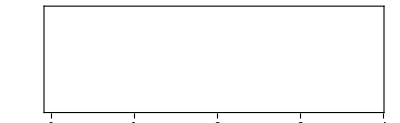

```mathematica
combinedTimeline[<|"periods"->"", "historicalCountries"->"", "militaryConflicts"->"", "persons"->""|>]
```

```mathematica
combinedTimeline[<|"periods"->"Roman Era", "historicalCountries"->"", "militaryConflicts"->"", "persons"->""|>]
```

{{Roman Greek Period},{},{},{}}

-Graphics-

```mathematica
combinedTimeline[<|"periods"->"Roman Era", "militaryConflicts"->"Punic Wars", "persons"->"Julius Caesar;Cleopatra"|>]
```

{{Roman Greek Period},{},{},{DateInterval[…]Julius Caesar,DateInterval[…]Cleopatra}}

-Graphics-

```mathematica
combinedTimeline[<|"persons"->"Marx;Engels;Lenin"|>]
```

{{},{},{},{DateInterval[…]Karl Marx,DateInterval[…]Friedrich Engels,DateInterval[…]Vladimir Lenin}}

-Graphics-

```mathematica
combinedTimeline[<|"persons"->"Marx;Engels;Lenin", "militaryConflicts"->"World War II;Russian Civil War", "historicalCountries"->"Soviet Union"|>]
```

{{},{DateInterval[…]Union of Soviet Socialist Republics},{World War II,Russian Civil War},{DateInterval[…]Karl Marx,DateInterval[…]Friedrich Engels,DateInterval[…]Vladimir Lenin}}

-Graphics-

```mathematica
toEntityHistoricalCountryString["Soviet union"]
```

Union of Soviet Socialist Republics 1922 - 1991

```mathematica
combinedTimeline[<|"periods"->"Atomic Age","historicalCountries"->"Soviet Union", "persons"->"Donald Trump"|>]
```

{{Atomic Age},{DateInterval[…]Union of Soviet Socialist Republics},{},{DateInterval[…]Donald Trump}}

-Graphics-

```mathematica
combinedTimeline[<|"historicalCountries"->"Hungary"|>]
```

{{},{DateInterval[…]Hungary},{},{}}

-Graphics-

```mathematica
TimelinePlot[{{},{DateInterval[…]"Hungary"},{},{}},PlotTheme->"Web",PlotLayout->"Stacked",Filling->Axis,PlotLegends->{"Periods","Historical Countries","Military Conflicts","Persons"},ImageSize->Large]
```

TimelinePlot[{{},{DateInterval[…]Hungary},{},{}},PlotTheme→Web,PlotLayout→Stacked,Filling→Axis,PlotLegends→{Periods,Historical Countries,Military Conflicts,Persons},ImageSize→Large]

```mathematica
TimelinePlot[{Entity["HistoricalCountry","Hungary"]}]
```

-Graphics-

```mathematica
TimelinePlot[{DateInterval[…]}]
```

-Graphics-

```mathematica
TimelinePlot[{DateInterval[{DateObject[{1973}],InfiniteFuture}]}]
```

-Graphics-

```mathematica
Labeled[DateInterval[{DateObject[{1973}],InfiniteFuture}],"Sic"]
```

DateInterval[…]Sic

```mathematica
TimelinePlot[{{Labeled[DateInterval[{DateObject[{1973}],InfiniteFuture}],"Sic"]},{ DateInterval[{DateObject[{1973}],Now}]}}, Filling->Axis]
```

TimelinePlot[{{DateInterval[…]Sic},{DateInterval[…]}},Filling→Axis]

```mathematica
TimelinePlot[{{DateInterval[{DateObject[{1973}],InfiniteFuture}]},{ DateInterval[{DateObject[{1973}],Now}]}}, Filling->Axis]
```

TimelinePlot[{{DateInterval[…]},{DateInterval[…]}},Filling→Axis]

```mathematica
TimelinePlot[{{ DateInterval[{DateObject[{1973}],Now}]}}, Filling->Axis]
```

-Graphics-

```mathematica
Now
```

Thu 18 Jul 2024 23:49:52GMT-7

# clean version

```mathematica
combinedTimeline = APIFunction[{
"periods" -> DelimitedSequence["String",";"]->{},
"historicalCountries" -> DelimitedSequence["String", ";"]->{},
"militaryConflicts"->DelimitedSequence["String",";"]->{},
"persons"->DelimitedSequence["String", ";"]->{}},
TimeConstrained[
Module[{periods, historicalCountries, historicalCountriesForTimeline, militaryConflicts, persons, personsForTimeline, imageURL}, 
periods = Interpreter["HistoricalPeriod"][#]&/@#periods // DeleteMissing;
historicalCountries = toEntityHistoricalCountryString /@ #historicalCountries // DeleteMissing;
historicalCountriesForTimeline = Labeled[DateInterval[{EntityValue[#,"StartDate"],If[MissingQ[EntityValue[#,"EndDate"]],Now, EntityValue[#,"EndDate"]]}],EntityValue[#,"Name"]]&/@ historicalCountries;
militaryConflicts = toEntityMilitaryConflictString /@ #militaryConflicts // DeleteMissing;
persons = Interpreter["Person"][#]&/@#persons //DeleteMissing;
personsForTimeline = Labeled[DateInterval[{EntityValue[#,"BirthDate"],If[MissingQ[EntityValue[#,"DeathDate"]],Now, EntityValue[#,"DeathDate"]]}],EntityValue[#,"Name"]]&/@persons;
Echo[{periods,historicalCountriesForTimeline,militaryConflicts,personsForTimeline}];
imageURL = CloudExport[
Rasterize[
TimelinePlot[{periods,historicalCountriesForTimeline,militaryConflicts,personsForTimeline},PlotTheme->"Web",PlotLayout->"Stacked", Filling-> Axis, PlotLegends->{"Periods","Historical Countries", "Military Conflicts", "Persons"}, ImageSize->Large],
ImageResolution->300],
"PNG", Permissions->"Public"][[1]];
ExportString[<|"image"->imageURL|>,"RawJSON"]
]
,28,Failure["TimeConstrained",<|"MessageTemplate"->"Request timed out"|>]]&, {"String", "JSON", "JSON"}]
```

APIFunction[{periods→DelimitedSequence[String,;]→{},historicalCountries→DelimitedSequence[String,;]→{},militaryConflicts→DelimitedSequence[String,;]→{},persons→DelimitedSequence[String,;]→{}},TimeConstrained[Module[{periods,historicalCountries,historicalCountriesForTimeline,militaryConflicts,persons,personsForTimeline,imageURL},periods=DeleteMissing[(Interpreter[HistoricalPeriod][#1]&)/@#periods];historicalCountries=DeleteMissing[toEntityHistoricalCountryString/@#historicalCountries];historicalCountriesForTimeline=(DateInterval[{EntityValue[#1,StartDate],If[MissingQ[EntityValue[#1,EndDate]],Now,EntityValue[#1,EndDate]]}]EntityValue[#1,Name]&)/@historicalCountries;militaryConflicts=DeleteMissing[toEntityMilitaryConflictString/@#militaryConflicts];persons=DeleteMissing[(Interpreter[Person][#1]&)/@#persons];personsForTimeline=(DateInterval[{EntityValue[#1,BirthDate],If[MissingQ[EntityValue[#1,DeathDate]],Now,EntityValue[#1,DeathDate]]}]EntityValue[#1,Name]&)/@persons;Echo[{periods,historicalCountriesForTimeline,militaryConflicts,personsForTimeline}];imageURL=CloudExport[Rasterize[TimelinePlot[{periods,historicalCountriesForTimeline,militaryConflicts,personsForTimeline},PlotTheme→Web,PlotLayout→Stacked,Filling→Axis,PlotLegends→{Periods,Historical Countries,Military Conflicts,Persons},ImageSize→Large],ImageResolution→300],PNG,Permissions→Public]⟦1⟧;ExportString[Association[image→imageURL],RawJSON]],28,Failure[TimeConstrained,Association[MessageTemplate→Request timed out]]]&,{String,JSON,JSON}]